```mathematica
Quiet[Remove["Global`*"],{Remove::rmnsm}];Print["Mathematica $Version = “",$Version,"”"];Print["Execution started at = ",DateString[DateList[],{"Hour",":","Minute"," on ","DayNameShort"," ","Day"," ","MonthNameShort"," ","Year"}]];
```

Mathematica $Version = “9.0 for Mac OS X x86 (64-bit) (January 24, 2013)”

Execution started at = 21:18 on Tue 29 Jun 2021

```mathematica
w=420 360/127-48;h=297 360/127-48-6;
rApproximation=(r≤124);
```

```mathematica
If[NumericQ[h]&&NumericQ[w],Print[N[h/w,20]]];
```

0.68958815745947734039

```mathematica
rKnownPoly=Module[{poly},
	poly=Factor[GroebnerBasis[{
		h==2r+gR(nR-1),
		w==2gC nSC+2r(nC-2nSC),
		gR^2+gC^2==4 r^2},{r},{gR,gC}]⟦1⟧];
	poly
]/.{nSC->1,nC->5,nR->5};
```

```mathematica
rKnown=r/.Solve[0==rKnownPoly,r]⟦1⟧;N[rKnown,8]
```

122.46582

```mathematica
(* rKnown concurs with answer of “122.466” reported by the PostScript software. E.g.: *)
Map[Print[Hyperlink["http://www.jdawiseman.com/"<>StringTake[#,4]<>"/"<>#<>".pdf"]]&,{"20191121_Rebello_Valente","20191023_Messias","20190611_1994s","20190501_Broadbent","20180605_Eights","20180508_Sixties","20180410_1963s","20171010_Gould_Campbell","20170608_1967s"}];
```

```mathematica
Hyperlink["http://hydra.nat.uni-magdeburg.de/packing/crc_700/crc14_0.700000000000.html"]
```

```mathematica
-Graphics-     ;
```

```mathematica
posns={{r, r}, {r, y2}, {r, h-r}, {x4, (y2+r)/2}, {x5, (y2+h-r)/2}, {2x4-r, r}, {x4+x5-r, h/2}, {2x5-r, h-r}, {w/2+x4-r, y9}, {w/2+x4-r, y9+2r}, {2x5+r, h-r}, {w-r, r}, {w-r, 3r}, {w-r, 5.0170243r (* rattler *)}}  ;
```

```mathematica
touchers={
	{1,4},
	{2,4},
	{2,5}, 
	{3,5},
	{4,6},
	{4,7}, 
	{5,7},
	{5,8},
	{6,9},
	{7,10},
	{8,11},
	{9,10},
	{9,12},
	{10,11} ,
	{10,13},
	{12,13}
};
```

```mathematica
vars=Variables[Flatten[posns]];
$Assumptions=Apply[And,Map[#∈Reals&&#>0&,vars]]
```

r∈Reals&&r>0&&x4∈Reals&&x4>0&&x5∈Reals&&x5>0&&y2∈Reals&&y2>0&&y9∈Reals&&y9>0

```mathematica
conditionsProto=Map[Simplify[Apply[Plus,(posns⟦#⟦1⟧⟧-posns⟦#⟦2⟧⟧)^2]==4r^2]&,touchers];
```

```mathematica
conditions=Apply[And,conditionsProto//DeleteDuplicates//FullSimplify//DeleteDuplicates]//Simplify;
(* http://mathematica.stackexchange.com/questions/146292/ *)
```

```mathematica
Print[vars," = vars;\n",
	Length[vars]," = Length[vars];\n",
	Length[touchers]," = Length[touchers];\n",
	Length[conditionsProto]," = Length[conditionsProto]\n",
	Length[conditions]," = Length[conditions]."
]
```

{r,x4,x5,y2,y9} = vars;
5 = Length[vars];
16 = Length[touchers];
16 = Length[conditionsProto]
7 = Length[conditions].

```mathematica
easyBounds=(
	r>rKnown  &&  rApproximation
	&&y2≥3r  &&  y2≤h-3r
	&&x4>r  &&  x4≤r (Sqrt[3]+1)  &&  x4<w/2
	&&x5>r  &&  x5≤r (Sqrt[3]+1)  &&  x5<w/2
	&&y9>r  &&  y9≤r (Sqrt[3]+1)  &&  y9<h/2
);
```

```mathematica
(* Calc time ≈ 4.bd minutes on a 2.7 GHz Intel Core i5 *)
solution=FindInstance[conditions&&easyBounds,vars,Reals]⟦1⟧;
```

```mathematica
Print[solutionN=N[solution,30]];posnsNew=posns/.solutionN;rBest=r/.solutionN;
```

{r→123.024542592996512906027189627,x4→330.309804633144305248629269789,x5→326.488110592899628218843767612,y2→388.150719812910558563238967901,y9→172.780369766975963048528414029}

```mathematica
distanceSq=Flatten[Table[{j,i,((posnsNew⟦i,1⟧-posnsNew⟦j,1⟧)^2+(posnsNew⟦i,2⟧-posnsNew⟦j,2⟧)^2)/r^2}/.solutionN,{i,1,Length[posns]},{j,1,i-1}],1];
```

```mathematica
(* Errors, number too close *)
Length[Select[distanceSq,Last[#]<4&]]
```

0

```mathematica
(* Touchers *)
Length[Select[distanceSq,Abs[Last[#]-4]<10^-8&]]
```

16

```mathematica
(* Percentage improvement *)
{rBest/rKnown-1,  Log[rBest/rKnown]}*100
```

{0.456225932857837905900900336,0.455188376884860357055269969}

```mathematica
(* mm improvement in diameter *)
2(rBest-rKnown)127/360
```

0.394208591068554422506887108

```mathematica
(* How slight is the asymmetry? *)
{(y2/.solutionN)/h,   (h/2-y2/.solutionN)127/360}
```

{0.49264597365872799801654323243,2.044051621556552951301808546}

```mathematica
(* Rattler to nearest neighbours, in radii *)
Map[{#⟦1⟧,#⟦2⟧,Sqrt[#⟦3⟧]}&,Select[distanceSq,#⟦2⟧==14&&Last[#]<7&]]//MatrixForm
```

(10 | 14 | 2.5371
11 | 14 | 2.01702
13 | 14 | 2.01702)

```mathematica
(* Where should the rattler have been placed? *)
((y14/r)/.Solve[(y14-3r)^2==(2x5+2r-w)^2+(h-r-y14)^2,y14]⟦1⟧)/.solutionN
```

5.017024309129192968688550876

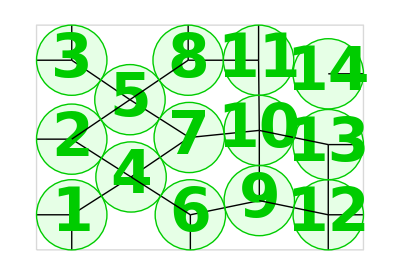

```mathematica
layoutImage=Graphics[Flatten[{
	{{EdgeForm[{AbsoluteThickness[1],LightGray}],FaceForm[None],Rectangle[{0,0},{w,h}]}},
	Map[{RGBColor[0.9,1.0,0.9],Disk[#,rBest]}&,posnsNew],
	Map[Text[Style[ToString[#],FontSize->60,Bold,RGBColor[0,0.8,0]],posnsNew⟦#⟧]&,Table[i,{i,1,Length[posnsNew]}]],
	Map[{AbsoluteThickness[1],Black,Line[{#,{0,#⟦2⟧}}]}&,Select[posnsNew,Abs[#⟦1⟧-r/.solutionN]<10^-6&]],
	Map[{AbsoluteThickness[1],Black,Line[{#,{#⟦1⟧,0}}]}&,Select[posnsNew,Abs[#⟦2⟧-r/.solutionN]<10^-6&]],
	Map[{AbsoluteThickness[1],Black,Line[{#,{w/.solutionN,#⟦2⟧}}]}&,Select[posnsNew,Abs[#⟦1⟧+r-w/.solutionN]<10^-6&]],
	Map[{AbsoluteThickness[1],Black,Line[{#,{#⟦1⟧,h/.solutionN}}]}&,Select[posnsNew,Abs[#⟦2⟧+r-h/.solutionN]<10^-6&]] ,
	Map[{AbsoluteThickness[1],Black,Line[{posnsNew⟦#⟦1⟧⟧,posnsNew⟦#⟦2⟧⟧}]}&,Select[distanceSq,Abs[Last[#]-4]<10^-8&]],
	Map[{AbsoluteThickness[1],RGBColor[0.0,0.8,0.0],Circle[#,rBest]}&,posnsNew],
	Map[{AbsoluteThickness[3],Red,Line[{posnsNew⟦#⟦1⟧⟧,posnsNew⟦#⟦2⟧⟧}]}&,Select[distanceSq,Last[#]≤4-10^-8&]]
},1],ImageSize->Scaled[0.6]]
```

```mathematica
(* Possible element of PackingStyles, for margins precisely as above *)
"[ /Array /Positions "  <>  StringJoin[Map["[" <> (#⟦1⟧//N//ToString) <> " " <> (#⟦2⟧//N//ToString) <> "] "&,posnsNew]]  <>  "]"
```

[ /Array /Positions [123.025 123.025] [123.025 388.151] [123.025 664.865] [330.31 255.588] [326.488 526.508] [537.595 123.025] [533.773 393.945] [529.952 664.865] [778.561 172.78] [778.561 418.829] [776.001 664.865] [1019.53 123.025] [1019.53 369.074] [1019.53 617.217] ]

```mathematica
(* Possible element of PackingStyles, being left-right mirror of previous *)
"[ /Array /Positions "  <>  StringJoin[Map["[" <> ((w-#⟦1⟧)//N//ToString) <> " " <> (#⟦2⟧//N//ToString) <> "] "&,posnsNew]]  <>  "]"
```

[ /Array /Positions [1019.53 123.025] [1019.53 388.151] [1019.53 664.865] [812.241 255.588] [816.063 526.508] [604.956 123.025] [608.778 393.945] [612.6 664.865] [363.99 172.78] [363.99 418.829] [366.55 664.865] [123.025 123.025] [123.025 369.074] [123.025 617.217] ]